```mathematica
f[x_]:=Sin[x]-x/13
```

```mathematica
g[x_]:=x
h[x_] :=x/(1-x^2)
l[x_]:=x+0.5f[x]
l2[x_]:=x+2f[x]
l3[x_]:=x+4f[x]
l4[x_]:=x+10f[x]
l5[x_]:=x+20f[x]
```

```mathematica
NSolve[f[x]==0,x,Reals]
```

{{x→-8.69239},{x→-6.83698},{x→-2.91541},{x→0.},{x→2.91541},{x→6.83698},{x→8.69239}}

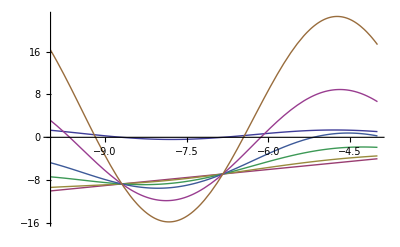

```mathematica
Plot[{f[x],g[x],l[x], l2[x], l3[x], l4[x], l5[x]},{x,-10,-4}]
```

```mathematica
i[x_]:=x+1h[x]
```

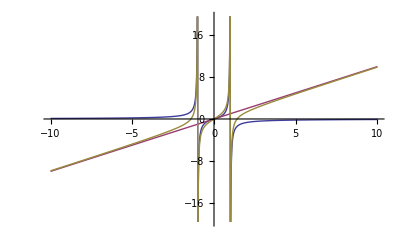

```mathematica
Plot[{h[x],g[x], i[x]},{x,-10,10}]
```

```mathematica
NSolve[h[x]==0,x,Reals]
```

{{x→0.}}

```mathematica
l[l[l[l[l[l[l[l[l[l[l[l[l[l[-10]]]]]]]]]]]]]]//N
```

-8.69287